```mathematica
GenerateValue[M0_,sigma_]:=If[sigma==0,M0,RandomVariate[NormalDistribution[M0,sigma]]]
ΔmProton = 0.00029
mProton=GenerateValue[0.93827208943,ΔmProton]
CoupleEff = GenerateValue[0.0000853727272727272,0.000010835775045318799]
BestYukawa2Cs2Ms6MB2=CoupleEff
ΓMAMI=0.33*10^(-9)
ΔΓMAMI=0.03*10^(-9)
Δα=0.000000017*10^(-3)
α=GenerateValue[7.297525664*10^(-3),Δα]
fK =110.10*10^(-3)
fπ =92.07*10^(-3)
ΔΓtotal=0.05*10^(-6)
Γtotal=GenerateValue[1.31*10^(-6),ΔΓtotal]
ΔBR=0.22*10^(-4)
BR=GenerateValue[2.56*10^(-4),ΔBR]
Δmπ=0.0005*10^(-3)
mπ=GenerateValue[134.9768*10^(-3),Δmπ]
ΔmπA=0.00018*10^(-3)
mπA=GenerateValue[139.57039*10^(-3),ΔmπA]
ΔMη=0.017*10^(-3)
Mη = GenerateValue[547.862*10^(-3),ΔMη]

MηPrime = GenerateValue[957.78*10^(-3),0.06*10^(-3)]

Δmρ=0.23*10^(-3)
mρ=GenerateValue[775.26*10^(-3),Δmρ]
Δmω=0.13*10^(-3)
mω=GenerateValue[782.66*10^(-3),Δmω]
Δmϕ=0.016*10^(-3)
mϕ=GenerateValue[1019.461*10^(-3),Δmϕ]
ΔΓω =0.13*10^(-3)
Γω = GenerateValue[8.68*10^(-3),ΔΓω]
ΔΓρ=0.8*10^(-3)
Γρ = GenerateValue[149.1*10^(-3),ΔΓρ]
ΔΓϕ=0.013*10^(-3)
Γϕ = GenerateValue[4.249*10^(-3),ΔΓϕ]
maZero = 980*10^(-3)
ΔmKP=0.016*10^(-3)
mKP=GenerateValue[493.677*10^(-3),ΔmKP]
mN=GenerateValue[938.27208816*10^(-3),0.00000029*10^(-3)]
Δg=0.01
g =GenerateValue[0.70,Δg]
ΔzSmBm=0.01
zSmBm =GenerateValue[0.65,ΔzSmBm]
ΔϕP=0.5
GenerateValue[41.4,ΔϕP]
ϕP = (GenerateValue[41.4,ΔϕP])Degree
ΔϕV=0.1
ϕV =(GenerateValue[3.3,ΔϕV])Degree
ΔzNS=0.02
zNS = GenerateValue[0.83,ΔzNS]
gρπγ = g/3
gρηγ = g*zNS*Cos[ϕP]
gωπγ = g*Cos[ϕV]
gωηγ =g/3*(zNS*Cos[ϕP]*Cos[ϕV]-2*zSmBm*Sin[ϕP]*Sin[ϕV])
gϕπγ = g*Sin[ϕV]
gϕηγ =g/3*(zNS*Cos[ϕP]*Sin[ϕV]+2*zSmBm*Sin[ϕP]*Cos[ϕV])
cρ = gρπγ*gρηγ
cω = gωπγ*gωηγ
cϕ = gϕπγ*gϕηγ
```

0.00029

0.93842

0.0000840974

0.0000840974

3.3×10^-10

3.×10^-11

1.7×10^-11

0.00729753

0.1101

0.09207

5.×10^-8

1.31643×10^-6

0.000022

0.000227943

5.×10^-7

0.134977

1.8×10^-7

0.13957

0.000017

0.54786

0.957881

0.00023

0.775204

0.00013

0.782569

0.000016

1.01945

0.00013

0.0085792

0.0008

0.149215

0.000013

0.00423789

49/50

0.000016

0.493652

0.938272

0.01

0.700068

0.01

0.646349

0.5

40.9696

0.717673

0.1

0.0564599

0.02

0.828326

0.233356

0.436849

0.698952

0.13419

0.0395048

0.206282

0.101941

0.0937921

0.00814912

```mathematica
Ω2[Mx_,EnergyPhoton_]:=(√((-(mProton-Mx)^2+mProton^2+2*mProton*EnergyPhoton) (-(mProton+Mx)^2+mProton^2+2*mProton*EnergyPhoton)))/(8 π *(mProton^2+2*mProton*EnergyPhoton))
VBAloneBWtDARK[m132_,m232_,Yukawa2Cs2Ms6MB2_] := Abs[Yukawa2Cs2Ms6MB2*(4*64 mN^6)/α*cω]^2
VBAloneBWuDARK[m132_,m232_,Yukawa2Cs2Ms6MB2_] := Abs[Yukawa2Cs2Ms6MB2*(4*64 mN^6)/α*cω]^2
VBAloneBWtuDARK[m132_,m232_,Yukawa2Cs2Ms6MB2_]:=Re[(Yukawa2Cs2Ms6MB2*(4*64 mN^6)/α*cω)*Conjugate[(Yukawa2Cs2Ms6MB2*(4*64 mN^6)/α*cω)]]
MxCONSTRAINTm232MAX[Mx_,m132_] := ((Mx^2+mπ^2)^2)/(4 m132)-(-(-m132+Mx^2)/(2 √m132)+√(-mπ^2+((m132+mπ^2)^2)/(4 m132)))^2
MxCONSTRAINTm232MIN[Mx_,m132_] := ((Mx^2+mπ^2)^2)/(4 m132)-((-m132+Mx^2)/(2 √m132)+√(-mπ^2+((m132+mπ^2)^2)/(4 m132)))^2
MxConstraint[Mx_,m132_, m232_]:=HeavisideTheta[MxCONSTRAINTm232MAX[Mx,m132]-m232]*HeavisideTheta[m232-MxCONSTRAINTm232MIN[Mx,m132]]
MxBq2Bq2p[Mx_,m132_,m232_]:=1/8 (m132^2+Mx^4) (-m132-m232+Mx^2+mπ^2)^2 +1/8 (-m132+Mx^2) (-m232+Mx^2) (m132 m232+Mx^2 (m132+m232-Mx^2-2 mπ^2))
MxBq1Bq1[Mx_,m132_,m232_]:=1/8 (m232^2+Mx^4) (-m132-m232+Mx^2+mπ^2)^2 +1/8 (-m132+Mx^2) (-m232+Mx^2) (m132 m232+Mx^2 (m132+m232-Mx^2-2 mπ^2))
MxBq2Bq1[Mx_,m132_,m232_]:=1/8 (m132*m232+Mx^4) (-m132-m232+Mx^2+mπ^2)^2 +1/8 (-m132+Mx^2) (-m232+Mx^2) (m132 m232+Mx^2 (m132+m232-Mx^2-2 mπ^2))
ContinuousVBAloneMatrixVMDDARK[Mx_,m132_,m232_,Yukawa2Cs2Ms6MB2_] := (MxBq2Bq2p[Mx,m132,m232]*VBAloneBWtDARK[m132,m232,Yukawa2Cs2Ms6MB2]+2*MxBq2Bq1[Mx,m132,m232]*VBAloneBWtuDARK[m132,m232,Yukawa2Cs2Ms6MB2] +MxBq1Bq1[Mx,m132,m232]*VBAloneBWuDARK[m132,m232,Yukawa2Cs2Ms6MB2])*MxConstraint[Mx,m132, m232]

PartialContinuosΓ[Mx_,Yukawa2Cs2Ms6MB2_]:=(1/2)*1/(256 Mx^3 π^3)*NIntegrate[ContinuousVBAloneMatrixVMDDARK[Mx,m132,m232,Yukawa2Cs2Ms6MB2], {m132, mπ^2, Mx^2}, {m232, mπ^2, Mx^2} ,AccuracyGoal->30, Method->{"GlobalAdaptive"},MaxRecursion->100]
```

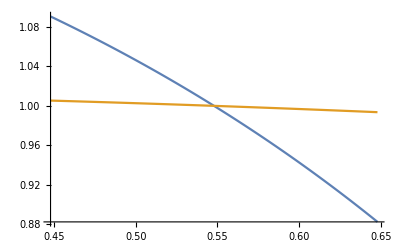

```mathematica
Plot[{Ω2[Mx,1.4]/Ω2[Mη,1.4],Ω2[Mx,11]/Ω2[Mη,11]},{Mx, Mη-0.1, Mη+0.1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000270341 and 1.25205×10^-8 for the integral and error estimates.

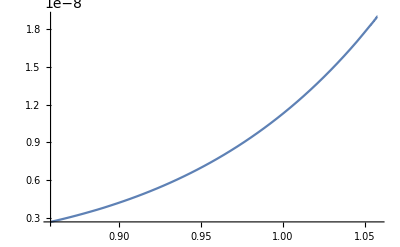

```mathematica
Plot[PartialContinuosΓ[Mx,CoupleEff],{Mx, MηPrime-0.1, MηPrime+0.1}]
```

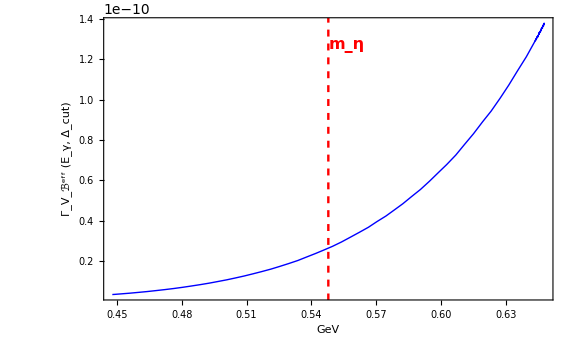

```mathematica
gammaLabel=Row[{Subsuperscript["Γ",Subscript["V","ℬ"],"eff"]," (",Subscript["E","γ"],", ",Subscript["Δ","cut"],")"}];

Plot[PartialContinuosΓ[Mx,CoupleEff],{Mx,Mη-0.1,Mη+0.1},Frame->{{True,False},{True,False}},Axes->False,FrameLabel->{Style["GeV",16,Black],Style[gammaLabel,16,Black]},RotateLabel->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive[Black,13],LabelStyle->Directive[Black],GridLines->{{Mη},None},GridLinesStyle->Directive[Red,Dashed,Thickness[0.003]],Epilog->{Inset[Style[Subscript["m","η"],16,Red,Bold],Scaled[{0.54,0.90}]]},PlotStyle->Directive[Blue,Thick],PlotRange->All,ImageSize->Large]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000270341 and 1.25205×10^-8 for the integral and error estimates.

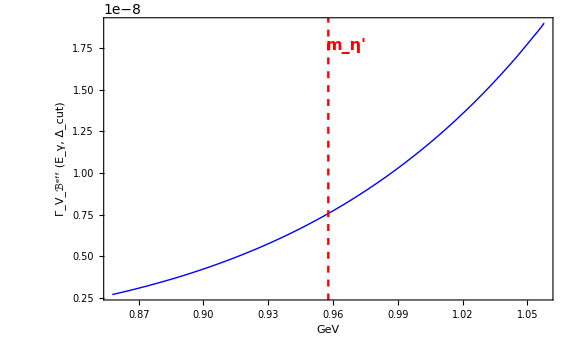

```mathematica
gammaLabel=Row[{Subsuperscript["Γ",Subscript["V","ℬ"],"eff"]," (",Subscript["E","γ"],", ",Subscript["Δ","cut"],")"}];
Plot[PartialContinuosΓ[Mx,CoupleEff],{Mx,MηPrime-0.1,MηPrime+0.1},Frame->{{True,False},{True,False}},Axes->False,FrameLabel->{Style["GeV",16,Black],Style[gammaLabel,16,Black]},RotateLabel->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive[Black,13],LabelStyle->Directive[Black],GridLines->{{MηPrime},None},GridLinesStyle->Directive[Red,Dashed,Thickness[0.003]],Epilog->{Inset[Style[Subscript["m",Superscript["η","′"]],16,Red,Bold],Scaled[{0.54,0.90}]]},PlotStyle->Directive[Blue,Thick],PlotRange->All,ImageSize->Large]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000270328 and 1.25596×10^-8 for the integral and error estimates.

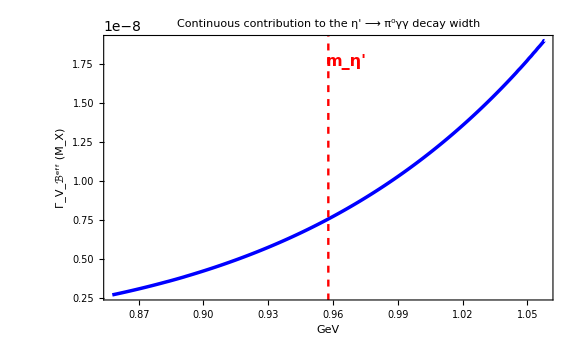

```mathematica
gammaLabel=Row[{Subsuperscript["Γ",Subscript["V","ℬ"],"eff"]," (",Subscript["M","X"],")"}];
titleLabel=Row[{"Continuous contribution to the ",Superscript["η","′"]," ⟶ ",Superscript["π","0"],"γγ decay width"}];
Plot[PartialContinuosΓ[Mx,CoupleEff],{Mx,MηPrime-0.1,MηPrime+0.1},Frame->{{True,False},{True,False}},Axes->False,PlotLabel->Style[titleLabel,16,Black,Bold],FrameLabel->{Style["GeV",16,Black],Style[gammaLabel,16,Black]},RotateLabel->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive[Black,13],LabelStyle->Directive[Black],GridLines->{{MηPrime},None},GridLinesStyle->Directive[Red,Dashed,Thickness[0.003]],Epilog->{Inset[Style[Subscript["m",Superscript["η","′"]],16,Red,Bold],Scaled[{0.54,0.90}]]},PlotStyle->Directive[Blue,AbsoluteThickness[2.5],CapForm["Round"],JoinForm["Round"]],PlotPoints->200,MaxRecursion->4,Exclusions->None,PerformanceGoal->"Quality",PlotRange->All,ImageSize->Large]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.36987×10^-9 and 4.48065×10^-12 for the integral and error estimates.

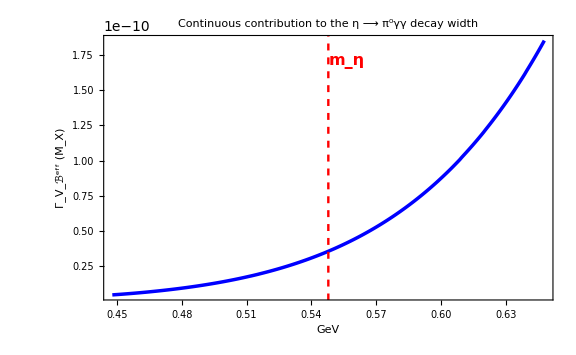

```mathematica
gammaLabel=Row[{Subsuperscript["Γ",Subscript["V","ℬ"],"eff"]," (",Subscript["M","X"],")"}];
titleLabel=Row[{"Continuous contribution to the ","η"," ⟶ ",Superscript["π","0"],"γγ decay width"}];
Plot[PartialContinuosΓ[Mx,CoupleEff],{Mx,Mη-0.1,Mη+0.1},Frame->{{True,False},{True,False}},Axes->False,PlotLabel->Style[titleLabel,16,Black,Bold],FrameLabel->{Style["GeV",16,Black],Style[gammaLabel,16,Black]},RotateLabel->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive[Black,13],LabelStyle->Directive[Black],GridLines->{{Mη},None},GridLinesStyle->Directive[Red,Dashed,Thickness[0.003]],Epilog->{Inset[Style[Subscript["m","η"],16,Red,Bold],Scaled[{0.54,0.90}]]},PlotStyle->Directive[Blue,AbsoluteThickness[2.5],CapForm["Round"],JoinForm["Round"]],PlotPoints->200,MaxRecursion->4,Exclusions->None,PerformanceGoal->"Quality",PlotRange->All,ImageSize->Large]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000270328 and 1.25596×10^-8 for the integral and error estimates.

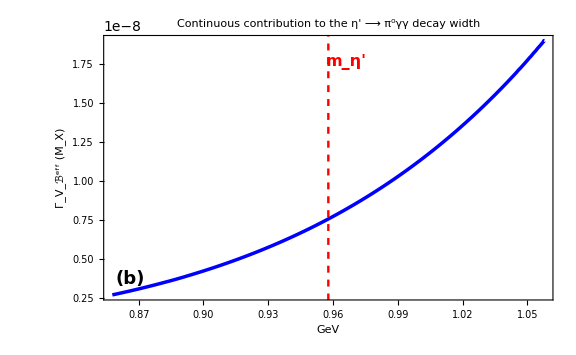

```mathematica
gammaLabel=Row[{Subsuperscript["Γ",Subscript["V","ℬ"],"eff"]," (",Subscript["M","X"],")"}];

titleLabel=Row[{"Continuous contribution to the ",Superscript["η","′"]," ⟶ ",Superscript["π","0"],"γγ decay width"}];

Plot[PartialContinuosΓ[Mx,CoupleEff],{Mx,MηPrime-0.1,MηPrime+0.1},Frame->{{True,False},{True,False}},Axes->False,PlotLabel->Style[titleLabel,16,Black,Bold],FrameLabel->{Style["GeV",16,Black],Style[gammaLabel,16,Black]},RotateLabel->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive[Black,13],LabelStyle->Directive[Black],GridLines->{{MηPrime},None},GridLinesStyle->Directive[Red,Dashed,Thickness[0.003]],Epilog->{Inset[Style[Subscript["m",Superscript["η","′"]],16,Red,Bold],Scaled[{0.54,0.90}]],Inset[Style["(b)",18,Black,Bold],Scaled[{0.06,0.08}]]},PlotStyle->Directive[Blue,AbsoluteThickness[2.5],CapForm["Round"],JoinForm["Round"]],PlotPoints->200,MaxRecursion->4,Exclusions->None,PerformanceGoal->"Quality",PlotRange->All,ImageSize->Large]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.36987×10^-9 and 4.48065×10^-12 for the integral and error estimates.

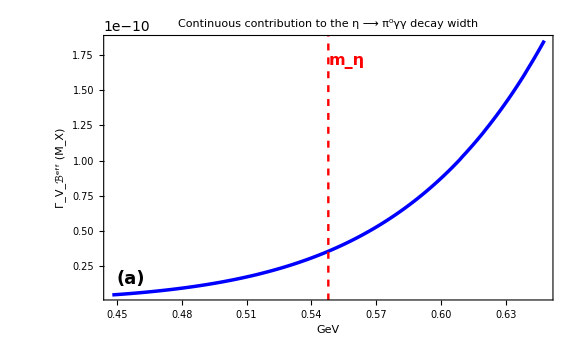

```mathematica
gammaLabel=Row[{Subsuperscript["Γ",Subscript["V","ℬ"],"eff"]," (",Subscript["M","X"],")"}];

titleLabel=Row[{"Continuous contribution to the ","η"," ⟶ ",Superscript["π","0"],"γγ decay width"}];

Plot[PartialContinuosΓ[Mx,CoupleEff],{Mx,Mη-0.1,Mη+0.1},Frame->{{True,False},{True,False}},Axes->False,PlotLabel->Style[titleLabel,16,Black,Bold],FrameLabel->{Style["GeV",16,Black],Style[gammaLabel,16,Black]},RotateLabel->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive[Black,13],LabelStyle->Directive[Black],GridLines->{{Mη},None},GridLinesStyle->Directive[Red,Dashed,Thickness[0.003]],Epilog->{Inset[Style[Subscript["m","η"],16,Red,Bold],Scaled[{0.54,0.90}]],Inset[Style["(a)",18,Black,Bold],Scaled[{0.06,0.08}]]},PlotStyle->Directive[Blue,AbsoluteThickness[2.5],CapForm["Round"],JoinForm["Round"]],PlotPoints->200,MaxRecursion->4,Exclusions->None,PerformanceGoal->"Quality",PlotRange->All,ImageSize->Large]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000270328 and 1.25596×10^-8 for the integral and error estimates.

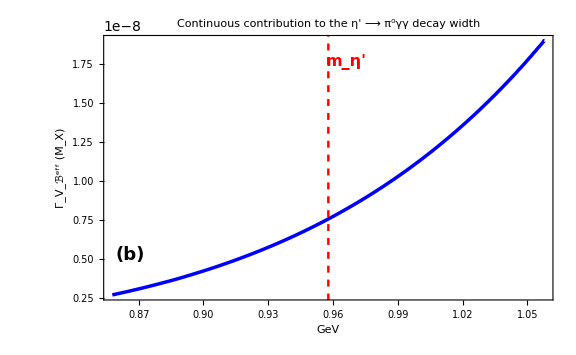

```mathematica
gammaLabel=Row[{Subsuperscript["Γ",Subscript["V","ℬ"],"eff"]," (",Subscript["M","X"],")"}];

titleLabel=Row[{"Continuous contribution to the ",Superscript["η","′"]," ⟶ ",Superscript["π","0"],"γγ decay width"}];

Plot[PartialContinuosΓ[Mx,CoupleEff],{Mx,MηPrime-0.1,MηPrime+0.1},Frame->{{True,False},{True,False}},Axes->False,PlotLabel->Style[titleLabel,16,Black,Bold],FrameLabel->{Style["GeV",16,Black],Style[gammaLabel,16,Black]},RotateLabel->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive[Black,13],LabelStyle->Directive[Black],GridLines->{{MηPrime},None},GridLinesStyle->Directive[Red,Dashed,Thickness[0.003]],Epilog->{Inset[Style[Subscript["m",Superscript["η","′"]],16,Red,Bold],Scaled[{0.54,0.90}]],Inset[Style["(b)",18,Black,Bold],Scaled[{0.06,0.17}]]},PlotStyle->Directive[Blue,AbsoluteThickness[2.5],CapForm["Round"],JoinForm["Round"]],PlotPoints->200,MaxRecursion->4,Exclusions->None,PerformanceGoal->"Quality",PlotRange->All,ImageSize->Large]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.36987×10^-9 and 4.48065×10^-12 for the integral and error estimates.

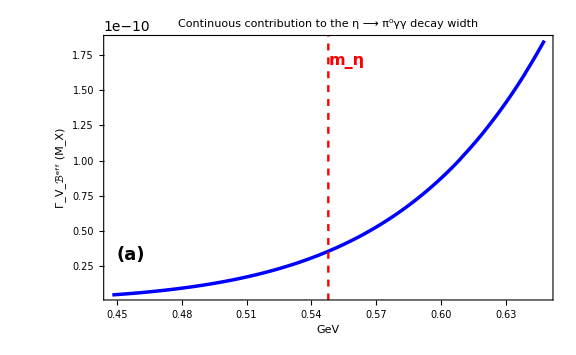

```mathematica
gammaLabel=Row[{Subsuperscript["Γ",Subscript["V","ℬ"],"eff"]," (",Subscript["M","X"],")"}];

titleLabel=Row[{"Continuous contribution to the ","η"," ⟶ ",Superscript["π","0"],"γγ decay width"}];

Plot[PartialContinuosΓ[Mx,CoupleEff],{Mx,Mη-0.1,Mη+0.1},Frame->{{True,False},{True,False}},Axes->False,PlotLabel->Style[titleLabel,16,Black,Bold],FrameLabel->{Style["GeV",16,Black],Style[gammaLabel,16,Black]},RotateLabel->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive[Black,13],LabelStyle->Directive[Black],GridLines->{{Mη},None},GridLinesStyle->Directive[Red,Dashed,Thickness[0.003]],Epilog->{Inset[Style[Subscript["m","η"],16,Red,Bold],Scaled[{0.54,0.90}]],Inset[Style["(a)",18,Black,Bold],Scaled[{0.06,0.17}]]},PlotStyle->Directive[Blue,AbsoluteThickness[2.5],CapForm["Round"],JoinForm["Round"]],PlotPoints->200,MaxRecursion->4,Exclusions->None,PerformanceGoal->"Quality",PlotRange->All,ImageSize->Large]
```

```mathematica
gammaLabel=Row[{Subsuperscript["Γ",Subscript["V","ℬ"],"eff"]," (",Subscript["M","X"],")"}];
titleLabel=Row[{"Continuous contribution to the ","η"," ⟶ ",Superscript["π","0"],"γγ decay width"}];

Plot[{1, Ω2[Mx]/Ω2[Mη],(PartialContinuosΓ[Mx,CoupleEff]/PartialContinuosΓ[Mη,CoupleEff]),(Ω2[Mx]/Ω2[Mη])*(PartialContinuosΓ[Mx,CoupleEff]/PartialContinuosΓ[Mη,CoupleEff])},{Mx,Mη-0.1,Mη+0.1},Frame->{{True,False},{True,False}},Axes->False,PlotLabel->Style[titleLabel,16,Black,Bold],FrameLabel->{Style["GeV",16,Black],Style[gammaLabel,16,Black]},RotateLabel->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive[Black,13],LabelStyle->Directive[Black],GridLines->{{Mη},None},GridLinesStyle->Directive[Red,Dashed,Thickness[0.003]],Epilog->{Inset[Style[Subscript["m","η"],16,Red,Bold],Scaled[{0.54,0.90}]],Inset[Style["(a)",18,Black,Bold],Scaled[{0.06,0.17}]]},PlotStyle->Directive[Blue,AbsoluteThickness[2.5],CapForm["Round"],JoinForm["Round"]],PlotPoints->200,MaxRecursion->4,Exclusions->None,PerformanceGoal->"Quality",PlotRange->All,ImageSize->Large]
```

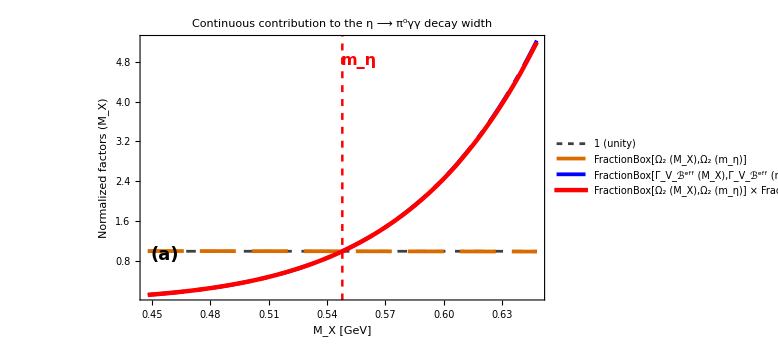

```mathematica
Clear[omegaRatio,widthRatio,productRatio,omegaReference,widthReference];

(*Evaluate normalization constants only once*)
omegaReference=N[Ω2[Mη]];

widthReference=Quiet[N[PartialContinuosΓ[Mη,CoupleEff]]];

(*Numerical wrappers prevent Plot from sending symbolic Mx to NIntegrate*)
omegaRatio[mx_?NumericQ]:=N[Ω2[mx]/omegaReference];

widthRatio[mx_?NumericQ]:=Quiet[N[PartialContinuosΓ[mx,CoupleEff]/widthReference]];

productRatio[mx_?NumericQ]:=omegaRatio[mx]*widthRatio[mx];


gammaLabel=Row[{"Normalized factors"," (",Subscript["M","X"],")"}];

titleLabel=Row[{"Continuous contribution to the ","η"," ⟶ ",Superscript["π","0"],"γγ decay width"}];


unityLegend=Style[Row[{"1"," ","(unity)"}],13,Black];

phaseSpaceLegend=Style[FractionBox[Row[{Subscript["Ω","2"]," (",Subscript["M","X"],")"}],Row[{Subscript["Ω","2"]," (",Subscript["m","η"],")"}]],13,Black];

widthLegend=Style[FractionBox[Row[{Subsuperscript["Γ",Subscript["V","ℬ"],"eff"]," (",Subscript["M","X"],")"}],Row[{Subsuperscript["Γ",Subscript["V","ℬ"],"eff"]," (",Subscript["m","η"],")"}]],13,Black];

productLegend=Style[Row[{FractionBox[Row[{Subscript["Ω","2"]," (",Subscript["M","X"],")"}],Row[{Subscript["Ω","2"]," (",Subscript["m","η"],")"}]]," × ",FractionBox[Row[{Subsuperscript["Γ",Subscript["V","ℬ"],"eff"]," (",Subscript["M","X"],")"}],Row[{Subsuperscript["Γ",Subscript["V","ℬ"],"eff"]," (",Subscript["m","η"],")"}]]}],13,Black];


lineStyles={Directive[GrayLevel[0.25],AbsoluteThickness[2.0],Dashing[{0.012,0.012}]],Directive[Darker[Orange,0.15],AbsoluteThickness[2.7],Dashing[{0.045,0.020}]],Directive[Blue,AbsoluteThickness[2.7],Dashing[{0.045,0.014,0.010,0.014}]],Directive[Red,AbsoluteThickness[3.2]]};


Plot[{1,omegaRatio[Mx],widthRatio[Mx],productRatio[Mx]},{Mx,Mη-0.1,Mη+0.1},Frame->{{True,False},{True,False}},Axes->False,PlotLabel->Style[titleLabel,16,Black,Bold],FrameLabel->{Style[Row[{Subscript["M","X"]," [GeV]"}],16,Black],Style[gammaLabel,16,Black]},RotateLabel->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive[Black,13],LabelStyle->Directive[Black],GridLines->{{Mη},None},GridLinesStyle->Directive[Red,Dashed,AbsoluteThickness[1.8]],Epilog->{Inset[Style[Subscript["m","η"],16,Red,Bold],Scaled[{0.54,0.90}]],Inset[Style["(a)",18,Black,Bold],Scaled[{0.06,0.17}]]},PlotStyle->lineStyles,PlotLegends->Placed[LineLegend[lineStyles,{unityLegend,phaseSpaceLegend,widthLegend,productLegend},LegendMarkerSize->42,LegendLayout->"Column",LegendFunction->(Framed[#,Background->White,FrameStyle->Directive[GrayLevel[0.75],Thin],FrameMargins->7,RoundingRadius->3]&)],{0.73,0.27}],PlotPoints->100,MaxRecursion->3,Exclusions->None,PerformanceGoal->"Quality",PlotRange->All,ImageSize->Large]
```

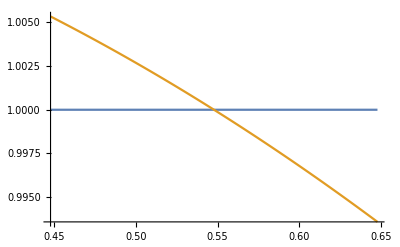

```mathematica
Plot[{1,Ω2[Mx]/Ω2[Mη]},{Mx, Mη-0.1, Mη+0.1}]
```

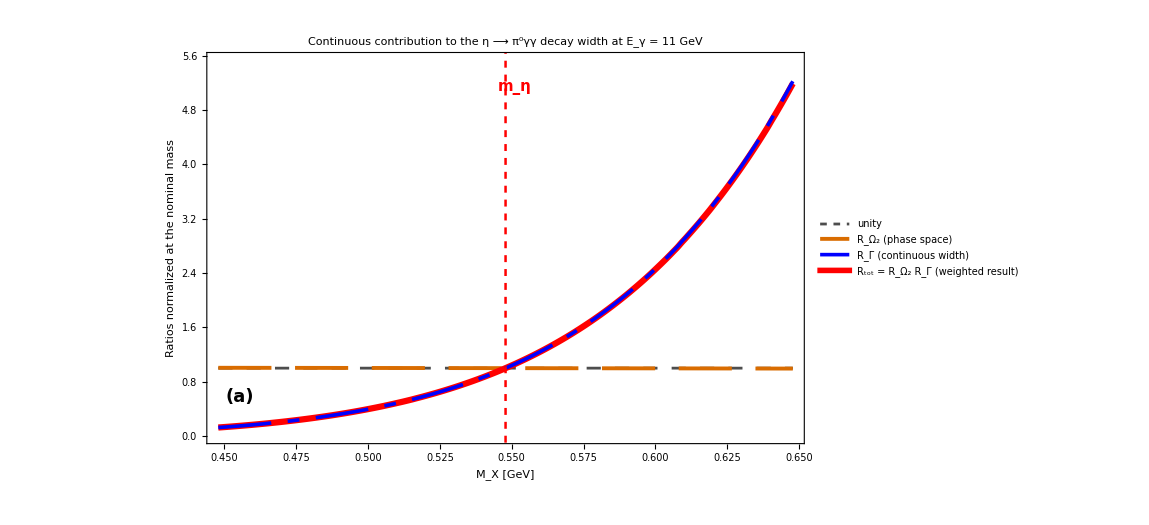

```mathematica
Clear[Ω2,omegaReference,widthReference,mxGrid,unityData,omegaData,widthData,productData,phaseInset,unityStyle,omegaStyle,widthStyle,productStyle];

(* ============================================================*)
(*JEF kinematics*)
(* ============================================================*)

EnergyPhotonJEF=11.0;

Ω2[Mx_?NumericQ,EnergyPhoton_?NumericQ]:=Sqrt[(-(mProton-Mx)^2+mProton^2+2*mProton*EnergyPhoton)*(-(mProton+Mx)^2+mProton^2+2*mProton*EnergyPhoton)]/(8*π*(mProton^2+2*mProton*EnergyPhoton));


(* ============================================================*)
(*Reference values at Mx=m_eta*)
(* ============================================================*)

mEtaReference=N[Mη];

omegaReference=N[Ω2[mEtaReference,EnergyPhotonJEF]];

widthReference=Quiet[N[PartialContinuosΓ[mEtaReference,CoupleEff]]];


(* ============================================================*)
(*Evaluate everything numerically before plotting*)
(* ============================================================*)

mxGrid=N[Subdivide[mEtaReference-0.1,mEtaReference+0.1,160]];

unityData=({#,1.0}&)/@mxGrid;

omegaData=({#,Ω2[#,EnergyPhotonJEF]/omegaReference}&)/@mxGrid;

widthData=({#,Quiet[N[PartialContinuosΓ[#,CoupleEff]/widthReference]]}&)/@mxGrid;

productData=MapThread[{#1[[1]],#1[[2]]*#2[[2]]}&,{omegaData,widthData}];


(* ============================================================*)
(*Plot ranges*)
(* ============================================================*)

mainYMaximum=1.06*Max[Flatten[{unityData[[All,2]],widthData[[All,2]],productData[[All,2]]}]];

omegaYMinimum=Min[omegaData[[All,2]]]-0.001;

omegaYMaximum=Max[omegaData[[All,2]]]+0.001;


(* ============================================================*)
(*Line styles*)
(* ============================================================*)

unityStyle=Directive[GrayLevel[0.3],AbsoluteThickness[2.0],Dashing[{0.012,0.012}]];

omegaStyle=Directive[Darker[Orange,0.15],AbsoluteThickness[2.8],Dashing[{0.045,0.020}]];

widthStyle=Directive[Blue,AbsoluteThickness[2.6],Dashing[{0.045,0.014,0.010,0.014}],CapForm["Round"]];

productStyle=Directive[Red,AbsoluteThickness[4.5],CapForm["Round"],JoinForm["Round"]];


(* ============================================================*)
(*Compact,properly rendered legend*)
(* ============================================================*)

plotLegend=LineLegend[{unityStyle,omegaStyle,widthStyle,productStyle},{Style["unity",12,Black],Style[Row[{Subscript["R",Subscript["Ω","2"]],"   (phase space)"}],12,Black],Style[Row[{Subscript["R","Γ"],"   (continuous width)"}],12,Black],Style[Row[{Subscript["R","tot"]," = ",Subscript["R",Subscript["Ω","2"]]," ",Subscript["R","Γ"],"   (weighted result)"}],12,Black]},LegendMarkerSize->36,LegendLayout->"Column",LegendFunction->(Framed[#,Background->White,FrameStyle->Directive[GrayLevel[0.75],AbsoluteThickness[0.8]],FrameMargins->6,RoundingRadius->3]&)];


(* ============================================================*)
(*Phase-space inset*)
(* ============================================================*)

phaseInset=ListLinePlot[{unityData,omegaData},PlotStyle->{unityStyle,omegaStyle},InterpolationOrder->2,Frame->True,Axes->False,PlotRange->{{mEtaReference-0.1,mEtaReference+0.1},{omegaYMinimum,omegaYMaximum}},PlotLabel->Style["Phase-space zoom",10,Black,Bold],FrameLabel->{Style[Subscript["M","X"],10,Black],Style[Subscript["R",Subscript["Ω","2"]],10,Black]},FrameStyle->Directive[Black,AbsoluteThickness[1.0]],FrameTicksStyle->Directive[Black,8],GridLines->{None,{1.0}},GridLinesStyle->Directive[GrayLevel[0.65],Dotted,AbsoluteThickness[1.0]],Epilog->{Directive[Red,Dashed,AbsoluteThickness[1.2]],Line[{{mEtaReference,omegaYMinimum},{mEtaReference,omegaYMaximum}}]},Background->White,ImageSize->245];


(* ============================================================*)
(*Final figure*)
(* ============================================================*)

ListLinePlot[{unityData,omegaData,(*Product is drawn before the width*)productData,widthData},PlotStyle->{unityStyle,omegaStyle,productStyle,widthStyle},InterpolationOrder->2,Frame->{{True,False},{True,False}},Axes->False,PlotRange->{{mEtaReference-0.1,mEtaReference+0.1},{0,mainYMaximum}},PlotLabel->Style[Row[{"Continuous contribution to the ","η"," ⟶ ",Superscript["π","0"],"γγ"," decay width at ",Subscript["E","γ"]," = 11 GeV"}],16,Black,Bold],FrameLabel->{Style[Row[{Subscript["M","X"]," [GeV]"}],16,Black],Style["Ratios normalized at the nominal mass",16,Black]},RotateLabel->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive[Black,13],LabelStyle->Directive[Black],GridLines->{{mEtaReference},None},GridLinesStyle->Directive[Red,Dashed,AbsoluteThickness[1.8]],PlotLegends->Placed[plotLegend,{0.23,0.70}],Epilog->{Inset[Style[Subscript["m","η"],15,Red,Bold],Scaled[{0.515,0.91}]],Inset[Style["(a)",18,Black,Bold],Scaled[{0.055,0.12}]],Inset[phaseInset,Scaled[{0.77,0.25}]]},PlotRangeClipping->True,ImagePadding->65,ImageSize->850]
```

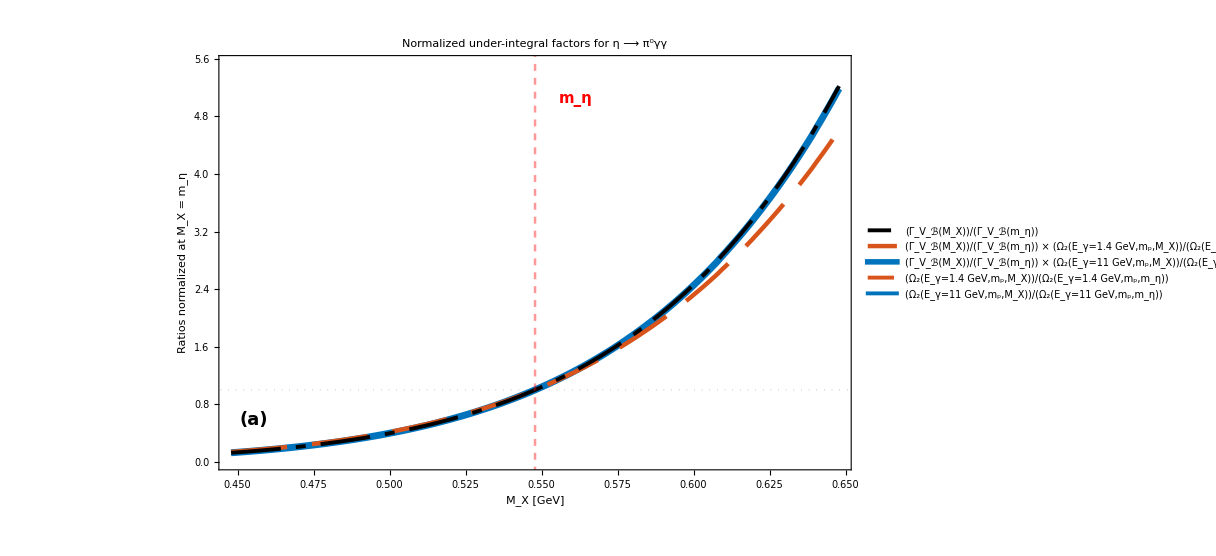

```mathematica
Clear[Ω2,omegaReferenceMAMI,omegaReferenceJEF,widthReference,mxGrid,omegaMAMIData,omegaJEFData,widthData,productMAMIData,productJEFData,phaseInset,omegaArgumentBox,omegaRatioBox,gammaArgumentBox,gammaRatioBox];


(* ============================================================*)
(*Energies and display range*)
(* ============================================================*)

EnergyPhotonMAMI=1.4;
EnergyPhotonJEF=11.0;

(*This is only the displayed M_X range—not Delta_cut*)
displayHalfRange=0.1;


(* ============================================================*)
(*Production phase space*)
(* ============================================================*)

Ω2[Mx_?NumericQ,EnergyPhoton_?NumericQ]:=Sqrt[(-(mProton-Mx)^2+mProton^2+2*mProton*EnergyPhoton)*(-(mProton+Mx)^2+mProton^2+2*mProton*EnergyPhoton)]/(8*π*(mProton^2+2*mProton*EnergyPhoton));


(* ============================================================*)
(*Reference values at M_X=m_eta*)
(* ============================================================*)

mEtaReference=N[Mη];

omegaReferenceMAMI=N[Ω2[mEtaReference,EnergyPhotonMAMI]];

omegaReferenceJEF=N[Ω2[mEtaReference,EnergyPhotonJEF]];

widthReference=Quiet[N[PartialContinuosΓ[mEtaReference,CoupleEff]]];


(* ============================================================*)
(*Numerical evaluation*)
(* ============================================================*)

mxGrid=N[Subdivide[mEtaReference-displayHalfRange,mEtaReference+displayHalfRange,160]];


(*Phase-space ratio at MAMI energy*)

omegaMAMIData=({#,Ω2[#,EnergyPhotonMAMI]/omegaReferenceMAMI}&)/@mxGrid;


(*Phase-space ratio at JEF energy*)

omegaJEFData=({#,Ω2[#,EnergyPhotonJEF]/omegaReferenceJEF}&)/@mxGrid;


(*Continuous-width ratio*)

widthData=({#,Quiet[N[PartialContinuosΓ[#,CoupleEff]/widthReference]]}&)/@mxGrid;


(*Width ratio multiplied by the MAMI phase-space ratio*)

productMAMIData=MapThread[{#1[[1]],#1[[2]]*#2[[2]]}&,{widthData,omegaMAMIData}];


(*Width ratio multiplied by the JEF phase-space ratio*)

productJEFData=MapThread[{#1[[1]],#1[[2]]*#2[[2]]}&,{widthData,omegaJEFData}];


(* ============================================================*)
(*Plot ranges*)
(* ============================================================*)

mainYMaximum=1.06*Max[Flatten[{widthData[[All,2]],productMAMIData[[All,2]],productJEFData[[All,2]],{1.0}}]];

phaseValues=Join[omegaMAMIData[[All,2]],omegaJEFData[[All,2]],{1.0}];

phaseRange=MinMax[phaseValues];

phasePadding=0.08*(phaseRange[[2]]-phaseRange[[1]]);

phaseYMinimum=phaseRange[[1]]-phasePadding;

phaseYMaximum=phaseRange[[2]]+phasePadding;


(* ============================================================*)
(*Line styles*)
(* ============================================================*)

widthStyle=Directive[Black,AbsoluteThickness[2.8],Dashing[{0.040,0.012,0.008,0.012}],CapForm["Round"]];

productMAMIStyle=Directive[RGBColor[0.85,0.33,0.10],AbsoluteThickness[3.2],Dashing[{0.045,0.020}],CapForm["Round"]];

productJEFStyle=Directive[RGBColor[0.00,0.45,0.74],AbsoluteThickness[5.0],CapForm["Round"],JoinForm["Round"]];

omegaMAMIStyle=Directive[RGBColor[0.85,0.33,0.10],AbsoluteThickness[2.8],Dashing[{0.045,0.020}],CapForm["Round"]];

omegaJEFStyle=Directive[RGBColor[0.00,0.45,0.74],AbsoluteThickness[2.8],CapForm["Round"]];


(* ============================================================*)
(*Explicit mathematical legend labels*)
(* ============================================================*)

omegaArgumentBox[energy_String,massBox_]:=RowBox[{SubscriptBox["Ω","2"],"(",SubscriptBox["E","γ"],"=",energy," ",StyleBox["GeV",FontSlant->"Plain"],",",SubscriptBox["m","p"],",",massBox,")"}];

omegaRatioBox[energy_String]:=FractionBox[omegaArgumentBox[energy,SubscriptBox["M","X"]],omegaArgumentBox[energy,SubscriptBox["m","η"]]];

gammaArgumentBox[massBox_]:=RowBox[{SubscriptBox["Γ",SubscriptBox["V","ℬ"]],"(",massBox,")"}];

gammaRatioBox=FractionBox[gammaArgumentBox[SubscriptBox["M","X"]],gammaArgumentBox[SubscriptBox["m","η"]]];


widthLegendLabel=Style[RawBoxes[gammaRatioBox],11,Black];

productMAMILegendLabel=Style[RawBoxes[RowBox[{gammaRatioBox," ","×"," ",omegaRatioBox["1.4"]}]],11,Black];

productJEFLegendLabel=Style[RawBoxes[RowBox[{gammaRatioBox," ","×"," ",omegaRatioBox["11"]}]],11,Black];

omegaMAMILegendLabel=Style[RawBoxes[omegaRatioBox["1.4"]],11,Black];

omegaJEFLegendLabel=Style[RawBoxes[omegaRatioBox["11"]],11,Black];


(*The legend contains all main-panel and inset curves explicitly*)

plotLegend=LineLegend[{widthStyle,productMAMIStyle,productJEFStyle,omegaMAMIStyle,omegaJEFStyle},{widthLegendLabel,productMAMILegendLabel,productJEFLegendLabel,omegaMAMILegendLabel,omegaJEFLegendLabel},LegendMarkerSize->48,LegendLayout->"Column",LegendFunction->(Framed[#,Background->White,FrameStyle->Directive[GrayLevel[0.75],AbsoluteThickness[0.8]],FrameMargins->8,RoundingRadius->3]&)];


(* ============================================================*)
(*Phase-space zoom*)
(* ============================================================*)

phaseInset=ListLinePlot[{omegaMAMIData,omegaJEFData},PlotStyle->{omegaMAMIStyle,omegaJEFStyle},InterpolationOrder->2,Frame->True,Axes->False,PlotRange->{{mEtaReference-displayHalfRange,mEtaReference+displayHalfRange},{phaseYMinimum,phaseYMaximum}},PlotLabel->Style["Production phase-space ratios",11,Black,Bold],FrameLabel->{Style[Row[{Subscript["M","X"]," [GeV]"}],10,Black],Style["Phase-space ratio",10,Black]},FrameStyle->Directive[Black,AbsoluteThickness[1.0]],FrameTicksStyle->Directive[Black,8],GridLines->{{{mEtaReference,Directive[Red,Dashed,AbsoluteThickness[1.2]]}},{{1.0,Directive[GrayLevel[0.55],Dotted,AbsoluteThickness[1.2]]}}},Epilog->{Inset[Style["(b)",13,Black,Bold],Scaled[{0.09,0.14}]]},Background->White,ImagePadding->42,ImageSize->300];


(* ============================================================*)
(*Final figure*)
(* ============================================================*)

ListLinePlot[{(*Draw the thick JEF curve first so that the other curves remain visible on top of it.*)productJEFData,productMAMIData,widthData},PlotStyle->{productJEFStyle,productMAMIStyle,widthStyle},InterpolationOrder->2,Frame->{{True,False},{True,False}},Axes->False,PlotRange->{{mEtaReference-displayHalfRange,mEtaReference+displayHalfRange},{0,mainYMaximum}},PlotLabel->Style[Row[{"Normalized under-integral factors for ","η"," ⟶ ",Superscript["π","0"],"γγ"}],16,Black,Bold],FrameLabel->{Style[Row[{Subscript["M","X"]," [GeV]"}],16,Black],Style[Row[{"Ratios normalized at ",Subscript["M","X"]," = ",Subscript["m","η"]}],16,Black]},RotateLabel->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive[Black,13],LabelStyle->Directive[Black],GridLines->{{{mEtaReference,Directive[Red,Dashed,AbsoluteThickness[1.8]]}},{{1.0,Directive[GrayLevel[0.55],Dotted,AbsoluteThickness[1.3]]}}},PlotLegends->Placed[plotLegend,Below],Epilog->{(*Offset prevents m_eta from touching the vertical line*)Inset[Style[Subscript["m","η"],15,Red,Bold],Offset[{24,0},{mEtaReference,0.91*mainYMaximum}],{-1,0}],Inset[Style["(a)",18,Black,Bold],Scaled[{0.055,0.12}]],Inset[phaseInset,Scaled[{0.23,0.70}]]},PlotRangeClipping->True,ImagePadding->70,ImageSize->900]
```